```mathematica
YJ={{0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},{30,68,75,82,82,77,68,68,58,51,50,41},{6,7,8,9,10,11,12,13,14,15,16},{38,35,28,25,18,15,12,10,7,7,4}}
```

{{0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},{30,68,75,82,82,77,68,68,58,51,50,41},{6,7,8,9,10,11,12,13,14,15,16},{38,35,28,25,18,15,12,10,7,7,4}}

```mathematica
YJ0=Union[Transpose[YJ[[{1,2}]]],Transpose[YJ[[{3,4}]]]]
```

{{0.25,30},{0.5,68},{0.75,75},{1,82},{1.5,82},{2,77},{2.5,68},{3,68},{3.5,58},{4,51},{4.5,50},{5,41},{6,38},{7,35},{8,28},{9,25},{10,18},{11,15},{12,12},{13,10},{14,7},{15,7},{16,4}}

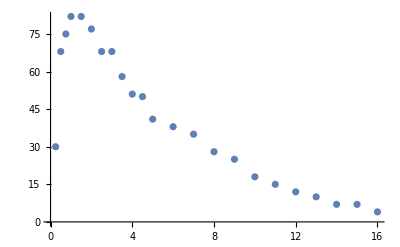

```mathematica
Gyj=ListPlot[YJ0]
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19}

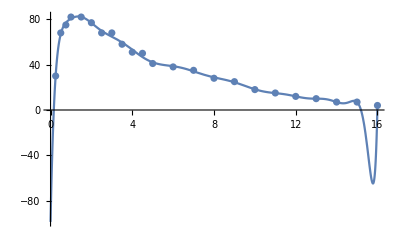

```mathematica
FF=Table[x^i,{i,0,19}]
exp=Fit[YJ0,FF,{x}];
Gyj1=Plot[exp,{x,0,16}];
Show[{Gyj1,Gyj},PlotRange->All]
```

```mathematica
slu=FindFit[YJ0,aa*x^bb*Exp[-cc*x],{aa,bb,cc},{x}]
```

{aa→98.7188,bb→0.468157,cc→0.295471}

```mathematica
exp=aa*x^bb*Exp[-cc*x]/.slu
```

98.7188 ⅇ^(-0.295471 x) x^0.468157

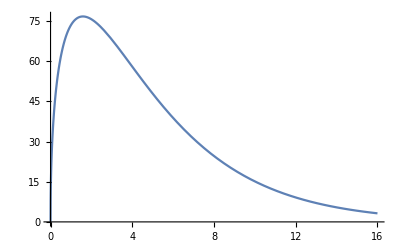
show[{-Graphics-,-Graphics-}]

```mathematica
Gyj2=Plot[exp,{x,0,16}];
show[{Gyj,Gyj2}]
```

```mathematica
slu=FindFit[YJ0,aa*x^bb*Exp[-cc*x]+aa1*x^bb1*Exp[-cc1*x],{aa,bb,cc,aa1,bb1,cc1},{x}]
```

{aa→38.4394,bb→1.04401,cc→0.311947,aa1→208.065,bb1→1.24437,cc1→1.3284}

```mathematica
exp=aa*x^bb*Exp[-cc*x]+aa1*x^bb1*Exp[-cc1*x]/.slu
```

38.4394 ⅇ^(-0.311947 x) x^1.04401+208.065 ⅇ^(-1.3284 x) x^1.24437

```mathematica
Gyj3=Plot[exp,{x,0,16},PlotStyle->Hue[0.9]];
show[{Gyj,Gyj2,Gyj3}]
```

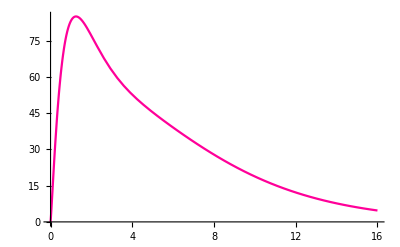
```mathematica
show[{-Graphics-,-Graphics-,-Graphics-}]
```